```mathematica
cal[nums_List,t_]:=Module[{ops,num=nums,rule,same,filter},ops={Plus,Subtract,Times,Divide};
rule=Thread[num->{x,y,z,w}];
same[a_,b_]:=Module[{p,q},p=a/.rule;
q=b/.rule;ReleaseHold[p]===ReleaseHold[q]];
filter[{op1_,op2_,op3_},{a_,b_,c_,d_}]:=Module[{ans={}},
If[Quiet@op1[op2[op3[a,b],c],d]==t,ans=num,
If[Quiet@op1[op2[a,b],op3[c,d]]==t,ans=num,
If[Quiet@op1[op2[a,op3[b,c]],d]==t,ans=num,
If[Quiet@op1[a,op2[b,op3[c,d]]]==t,ans=num]]]]
ans];
filter@@@Tuples[{Tuples[ops,3],Permutations[num]}]]
data=DeleteDuplicates[Sort/@Permutations[Table[ConstantArray[i,4],{i,1,6}]//Flatten,{4}]];
judge[nums_List,t_]:=If[Last[SortBy[cal[nums,t], Total]]≠{},nums]
f[n_]:=Module[{data,ansdata,result},
data=DeleteDuplicates[Sort/@Permutations[Table[ConstantArray[i,4],{i,1,n}]//Flatten,{4}]];
ansdata[t_]:=ParallelMap[judge[#,t]&,data];
result[t_]:=DeleteCases[ansdata[t],Null]//Length;
Table[result[k],{k,1,100}]//AbsoluteTiming]
```

```mathematica
For[i=2,i≤13,i++,Print[f[i]]]
```

{1.6713,{5,5,5,5,4,4,2,3,2,2,0,2,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

{4.2472,{15,15,15,15,14,14,12,13,12,11,7,11,5,5,7,7,3,8,2,4,5,1,0,6,2,1,4,1,1,4,0,0,1,0,0,4,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

{10.2968,{35,35,35,35,34,34,31,33,31,28,22,31,20,20,24,26,16,22,13,21,14,11,7,23,8,6,11,14,4,13,4,15,7,4,5,18,1,2,3,8,0,3,0,4,5,1,1,12,2,1,2,3,0,4,0,3,1,0,0,6,1,1,2,6,1,1,1,2,0,0,0,5,0,0,0,1,0,0,0,3,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,4,0,0,0,0}}

{23.2778,{70,70,68,70,69,69,64,66,65,63,55,62,46,47,58,58,43,48,40,53,40,34,27,53,35,27,32,36,20,41,18,34,20,14,26,38,9,9,12,34,6,16,6,16,27,7,5,29,8,19,6,10,3,13,13,10,3,2,2,28,2,2,8,12,9,3,1,4,3,10,1,14,1,1,12,5,2,3,2,16,5,1,1,6,4,0,1,2,0,9,0,2,0,0,4,9,1,1,1,11}}

{44.6489,{126,126,122,122,125,125,117,119,117,117,107,118,92,95,103,104,81,101,80,97,78,75,61,105,70,68,66,74,49,93,44,73,48,46,60,89,34,37,36,68,23,56,19,40,53,25,15,73,22,42,20,23,13,47,25,32,12,13,9,68,7,8,18,24,17,27,5,12,10,28,5,49,4,6,23,12,7,20,2,28,11,2,1,28,8,2,4,10,1,33,2,6,5,3,9,30,2,2,6,20}}

{80.8095,{206,209,202,195,203,207,199,195,194,191,178,196,167,176,174,170,140,164,143,164,150,135,117,170,126,119,122,145,103,154,92,128,95,95,130,150,76,80,78,124,67,123,61,81,96,58,54,133,77,81,55,55,39,90,59,88,38,38,28,111,25,26,65,52,43,56,21,28,25,76,16,89,15,16,41,27,41,38,12,52,24,13,9,78,20,9,13,25,8,61,29,15,12,8,18,55,6,33,16,32}}

{136.685,{318,328,314,311,311,318,309,309,300,302,274,304,260,282,276,285,229,252,215,264,232,219,195,275,192,193,197,242,168,234,153,225,160,161,203,240,124,136,141,222,124,201,112,151,159,114,107,234,135,145,106,116,80,155,109,180,84,90,67,185,62,75,124,140,84,105,52,74,57,135,43,173,38,42,71,63,70,79,29,126,45,33,23,124,39,24,29,78,22,104,52,39,26,20,33,127,18,62,36,57}}

{212.326,{467,492,470,460,456,463,457,455,453,447,417,444,386,409,414,425,353,405,335,385,354,315,297,404,300,300,332,350,255,337,236,328,266,242,297,375,202,204,232,324,193,285,169,241,278,187,173,340,216,224,186,186,149,277,187,275,159,152,120,276,117,136,238,224,145,176,97,126,123,211,99,293,92,96,137,116,125,143,79,208,143,80,60,203,79,59,77,131,60,206,88,73,65,43,58,196,42,95,107,97}}

{324.806,{663,709,675,662,662,656,646,653,644,647,599,637,554,597,592,606,509,591,496,586,508,474,420,566,431,454,465,504,373,522,350,463,373,364,428,529,300,326,336,496,281,415,248,360,412,299,254,462,308,378,279,284,227,412,290,391,235,247,197,440,192,230,338,331,237,282,159,213,203,368,169,421,158,179,225,198,203,237,145,374,226,158,116,308,157,130,135,223,117,358,153,141,118,113,120,292,85,170,178,227}}

{460.402,{900,980,926,906,898,894,873,879,878,879,841,870,779,812,799,818,702,795,691,794,714,712,606,756,602,611,640,664,543,702,504,641,583,509,592,709,431,456,479,670,403,554,387,560,562,414,364,611,429,508,404,404,341,556,464,539,340,341,313,590,292,323,460,457,353,460,266,312,310,508,268,566,241,271,342,310,364,348,238,513,339,235,204,440,254,212,225,400,201,491,254,223,193,189,206,416,158,261,334,339}}

{8942.69,{1215,1339,1265,1235,1215,1230,1179,1190,1183,1185,1136,1190,1064,1123,1093,1108,944,1088,918,1066,976,964,830,1068,809,820,853,909,709,944,660,868,798,691,776,1004,593,626,650,896,531,769,528,775,736,551,498,889,572,657,542,574,449,750,614,721,477,468,431,862,401,444,614,605,480,652,369,470,435,658,368,832,347,375,469,459,491,510,324,687,461,340,302,686,360,307,337,564,290,660,356,355,296,282,308,645,248,384,462,494}}

$Aborted

```mathematica
f[12]
```

{676.135,{1215,1339,1265,1235,1215,1230,1179,1190,1183,1185,1136,1190,1064,1123,1093,1108,944,1088,918,1066,976,964,830,1068,809,820,853,909,709,944,660,868,798,691,776,1004,593,626,650,896,531,769,528,775,736,551,498,889,572,657,542,574,449,750,614,721,477,468,431,862,401,444,614,605,480,652,369,470,435,658,368,832,347,375,469,459,491,510,324,687,461,340,302,686,360,307,337,564,290,660,356,355,296,282,308,645,248,384,462,494}}

```mathematica
f[13]
```

{930.417,{1565,1757,1644,1601,1563,1577,1527,1519,1526,1528,1470,1535,1414,1448,1438,1423,1240,1393,1197,1370,1252,1240,1108,1361,1074,1159,1134,1169,942,1190,890,1105,1033,892,1017,1266,821,830,948,1152,723,997,718,980,950,726,677,1137,762,843,725,847,633,928,795,915,647,613,590,1106,564,586,789,800,733,834,532,621,587,837,500,1053,495,497,634,613,687,769,456,876,598,453,447,873,507,424,466,724,395,864,569,497,426,388,437,829,373,519,611,654}}

```mathematica
data={{5,5,5,5,4,4,2,3,2,2,0,2,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{15,15,15,15,14,14,12,13,12,11,7,11,5,5,7,7,3,8,2,4,5,1,0,6,2,1,4,1,1,4,0,0,1,0,0,4,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{35,35,35,35,34,34,31,33,31,28,22,31,20,20,24,26,16,22,13,21,14,11,7,23,8,6,11,14,4,13,4,15,7,4,5,18,1,2,3,8,0,3,0,4,5,1,1,12,2,1,2,3,0,4,0,3,1,0,0,6,1,1,2,6,1,1,1,2,0,0,0,5,0,0,0,1,0,0,0,3,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,4,0,0,0,0},
{70,70,68,70,69,69,64,66,65,63,55,62,46,47,58,58,43,48,40,53,40,34,27,53,35,27,32,36,20,41,18,34,20,14,26,38,9,9,12,34,6,16,6,16,27,7,5,29,8,19,6,10,3,13,13,10,3,2,2,28,2,2,8,12,9,3,1,4,3,10,1,14,1,1,12,5,2,3,2,16,5,1,1,6,4,0,1,2,0,9,0,2,0,0,4,9,1,1,1,11},
{126,126,122,122,125,125,117,119,117,117,107,118,92,95,103,104,81,101,80,97,78,75,61,105,70,68,66,74,49,93,44,73,48,46,60,89,34,37,36,68,23,56,19,40,53,25,15,73,22,42,20,23,13,47,25,32,12,13,9,68,7,8,18,24,17,27,5,12,10,28,5,49,4,6,23,12,7,20,2,28,11,2,1,28,8,2,4,10,1,33,2,6,5,3,9,30,2,2,6,20},
{206,209,202,195,203,207,199,195,194,191,178,196,167,176,174,170,140,164,143,164,150,135,117,170,126,119,122,145,103,154,92,128,95,95,130,150,76,80,78,124,67,123,61,81,96,58,54,133,77,81,55,55,39,90,59,88,38,38,28,111,25,26,65,52,43,56,21,28,25,76,16,89,15,16,41,27,41,38,12,52,24,13,9,78,20,9,13,25,8,61,29,15,12,8,18,55,6,33,16,32},
{318,328,314,311,311,318,309,309,300,302,274,304,260,282,276,285,229,252,215,264,232,219,195,275,192,193,197,242,168,234,153,225,160,161,203,240,124,136,141,222,124,201,112,151,159,114,107,234,135,145,106,116,80,155,109,180,84,90,67,185,62,75,124,140,84,105,52,74,57,135,43,173,38,42,71,63,70,79,29,126,45,33,23,124,39,24,29,78,22,104,52,39,26,20,33,127,18,62,36,57},
{467,492,470,460,456,463,457,455,453,447,417,444,386,409,414,425,353,405,335,385,354,315,297,404,300,300,332,350,255,337,236,328,266,242,297,375,202,204,232,324,193,285,169,241,278,187,173,340,216,224,186,186,149,277,187,275,159,152,120,276,117,136,238,224,145,176,97,126,123,211,99,293,92,96,137,116,125,143,79,208,143,80,60,203,79,59,77,131,60,206,88,73,65,43,58,196,42,95,107,97},
{663,709,675,662,662,656,646,653,644,647,599,637,554,597,592,606,509,591,496,586,508,474,420,566,431,454,465,504,373,522,350,463,373,364,428,529,300,326,336,496,281,415,248,360,412,299,254,462,308,378,279,284,227,412,290,391,235,247,197,440,192,230,338,331,237,282,159,213,203,368,169,421,158,179,225,198,203,237,145,374,226,158,116,308,157,130,135,223,117,358,153,141,118,113,120,292,85,170,178,227},
{900,980,926,906,898,894,873,879,878,879,841,870,779,812,799,818,702,795,691,794,714,712,606,756,602,611,640,664,543,702,504,641,583,509,592,709,431,456,479,670,403,554,387,560,562,414,364,611,429,508,404,404,341,556,464,539,340,341,313,590,292,323,460,457,353,460,266,312,310,508,268,566,241,271,342,310,364,348,238,513,339,235,204,440,254,212,225,400,201,491,254,223,193,189,206,416,158,261,334,339},
{1215,1339,1265,1235,1215,1230,1179,1190,1183,1185,1136,1190,1064,1123,1093,1108,944,1088,918,1066,976,964,830,1068,809,820,853,909,709,944,660,868,798,691,776,1004,593,626,650,896,531,769,528,775,736,551,498,889,572,657,542,574,449,750,614,721,477,468,431,862,401,444,614,605,480,652,369,470,435,658,368,832,347,375,469,459,491,510,324,687,461,340,302,686,360,307,337,564,290,660,356,355,296,282,308,645,248,384,462,494},
{1565,1757,1644,1601,1563,1577,1527,1519,1526,1528,1470,1535,1414,1448,1438,1423,1240,1393,1197,1370,1252,1240,1108,1361,1074,1159,1134,1169,942,1190,890,1105,1033,892,1017,1266,821,830,948,1152,723,997,718,980,950,726,677,1137,762,843,725,847,633,928,795,915,647,613,590,1106,564,586,789,800,733,834,532,621,587,837,500,1053,495,497,634,613,687,769,456,876,598,453,447,873,507,424,466,724,395,864,569,497,426,388,437,829,373,519,611,654}};
```

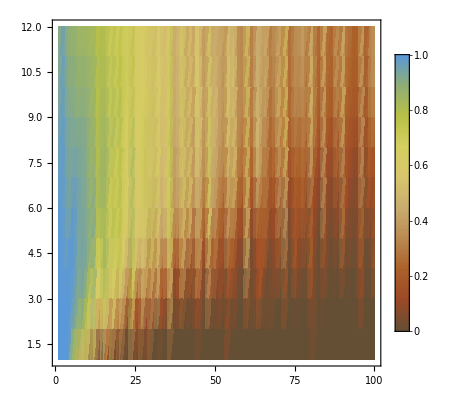
{-Graphics3D-,-Graphics-}

```mathematica
dataRatio=Divide[dataList,Binomial[#+3,4]&/@Range[2,13]]//N;
{ListPlot3D[dataRatio,Mesh->None,InterpolationOrder->3,ColorFunction->"SouthwestColors"],
ListDensityPlot[dataRatio,ColorFunction->"SouthwestColors",PlotLegends->Automatic]}
```

```mathematica
list2={5,5,5,5,4,4,2,3,2,2,0,2,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}/5 ;
list3={15,15,15,15,14,14,12,13,12,11,7,11,5,5,7,7,3,8,2,4,5,1,0,6,2,1,4,1,1,4,0,0,1,0,0,4,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0} /15;
list4={35,35,35,35,34,34,31,33,31,28,22,31,20,20,24,26,16,22,13,21,14,11,7,23,8,6,11,14,4,13,4,15,7,4,5,18,1,2,3,8,0,3,0,4,5,1,1,12,2,1,2,3,0,4,0,3,1,0,0,6,1,1,2,6,1,1,1,2,0,0,0,5,0,0,0,1,0,0,0,3,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,4,0,0,0,0} /35;
list10={663,709,675,662,662,656,646,653,644,647,599,637,554,597,592,606,509,591,496,586,508,474,420,566,431,454,465,504,373,522,350,463,373,364,428,529,300,326,336,496,281,415,248,360,412,299,254,462,308,378,279,284,227,412,290,391,235,247,197,440,192,230,338,331,237,282,159,213,203,368,169,421,158,179,225,198,203,237,145,374,226,158,116,308,157,130,135,223,117,358,153,141,118,113,120,292,85,170,178,227}/715; list13={1565,1757,1644,1601,1563,1577,1527,1519,1526,1528,1470,1535,1414,1448,1438,1423,1240,1393,1197,1370,1252,1240,1108,1361,1074,1159,1134,1169,942,1190,890,1105,1033,892,1017,1266,821,830,948,1152,723,997,718,980,950,726,677,1137,762,843,725,847,633,928,795,915,647,613,590,1106,564,586,789,800,733,834,532,621,587,837,500,1053,495,497,634,613,687,769,456,876,598,453,447,873,507,424,466,724,395,864,569,497,426,388,437,829,373,519,611,654}/1820;
{ListLinePlot[{list2,list3,list4,list10,list13},PlotTheme->"Detailed",PlotLegends->{"list2","list3","list4","list10","list13"}],
ListLinePlot[{list10,list13},PlotTheme->"Business",DataRange->{0,36},PlotRange->{0.1,1.0},PlotLegends->{"list10","list13"}]}
```

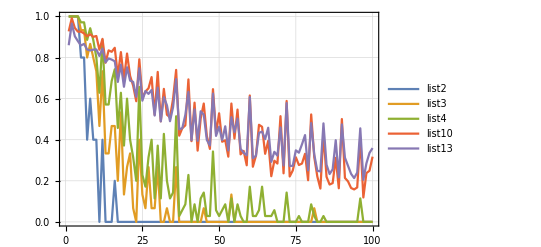
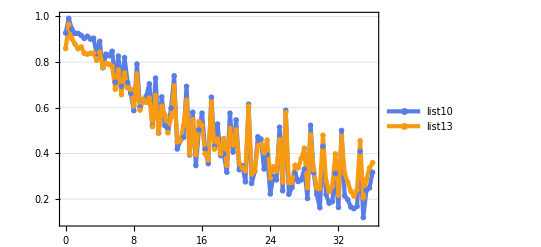
```mathematica
-Graphics-      -Graphics-
-Graphics3D-                     -Graphics-
```

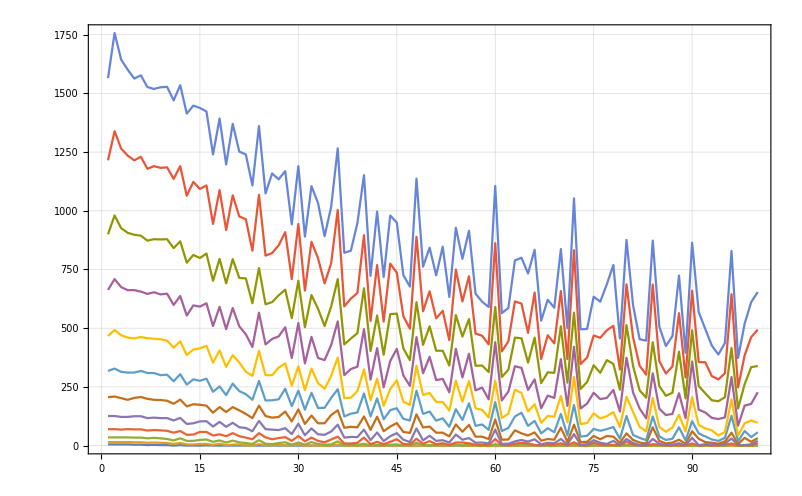

```mathematica
ListLinePlot[dataList,PlotTheme->"Detailed"]
ListLinePlot[dataRatio,PlotTheme->"Detailed"]
```